```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["Nekhaev_01.04.2019.xlsx"][[1]]
```

{{,Канал: 0,Канал : 1},{00:00:00,000,000,0.2393,1.7236},{00:00:00,000,100,0.2588,1.792},{00:00:00,000,200,0.2686,1.853},{00:00:00,000,300,0.2686,1.9214},2256,{00:00:00,226,000,0.4297,2.5781},{00:00:00,226,100,0.4297,2.4683},{00:00:00,226,200,0.4077,2.3706},{00:00:00,226,300,0.3979,2.2705}}
 |  |  |  |

```mathematica
data=data[[2;;All,2;;3]]
```

{{0.2393,1.7236},{0.2588,1.792},{0.2686,1.853},{0.2686,1.9214},{0.2783,1.9727},{0.2881,2.0508},{0.3003,2.0898},{0.3394,2.1509},{0.3198,2.1997},2246,{0.459,3.0273},{0.4395,2.937},{0.4492,2.8467},{0.4395,2.7686},{0.4297,2.6489},{0.4297,2.5781},{0.4297,2.4683},{0.4077,2.3706},{0.3979,2.2705}}
 |  |  |  |

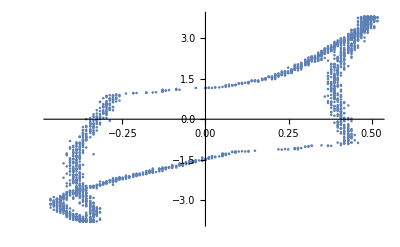

```mathematica
ListPlot[data]
```